### Styling

```mathematica
(*Styling of the text*)
st=Directive[FontSize->10,FontFamily->"CMU Serif"];
stylize[text_]:=Style[text,st];
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
```

### Recursive construction of the energy bands

```mathematica
rect[{x1_,x2_},δ_]:=Rectangle[{x1,-δ/2},{x2,+δ/2}];
```

```mathematica
(* takes spectra at step n-3 (g3), n-2 (g2) and n-1 (g1) and return spectra at step n-2, n-1 and n *)
rec[{g3_,g2_,g1_},ts_,tw_]:=Block[{z=tw/(2ts),zb=(tw/ts)^2,g},
g=Flatten [{zb g3,z g2 +ts,z g2 -ts},1];
{g2,g1,g}]
```

```mathematica
ts=1;
tw=0.5;
(* first three spectra corresponding resp to approximants ts, tw and twts *)
g0={{-2ts,2ts}};
g1={{-2tw,2tw}};
g2={{-ts-tw,-ts+tw},{ts-tw,ts+tw}};
```

### Recursive labeling of the gaps

```mathematica
(* susbstitution matrix *)
Ω={{1,1},{1,0}};
d=Inverse[Ω];
dm=d.d;
da=dm.d;
```

```mathematica
(* iterative construction of the gaps *)
lmol[g_]:=dm.g;
atom[g_]:=da.g+{1,-1};
rmol[g_]:=lmol[g]+{0,1};
(* count the number of states below gap g *)
count[g_,n_]:=g.{Fibonacci[n],Fibonacci[n-1]};
```

```mathematica
(* recursive labelling *)
recur[glist_]:=Flatten[Through[{lmol,atom,rmol}[#]]&/@glist,1]
```

```mathematica
(* initial conditions *)
(* initial transient gap at idos = 1/2 for the chain Subscript[F, 3] = 2 *)
G1={};
G2={};
gap0={0,1};
G3={gap0};
(* initial stable gaps at idos = 1/3, 2/3 for the chain Subscript[F, 4] = 3 *)
gapr={0,1};
gapl={1,-1};
G4={gapl,gapr};
(* Subscript[G, 5] *)
G5={{-1,2},gapl,gapr,{2,-2}};
(* return the list of gaps at step n (ordered by incresing energy) from the ordered list of gaps at step n-2 and n-3 *)
Gn[{Gm_,Ga_}]:=Join[lmol/@Gm,{gapl},atom/@Ga,{gapr},rmol/@Gm];
(* take {Subscript[G, n-3],Subscript[G, n-2],Subscript[G, n-1]}, return {Subscript[G, n-2],Subscript[G, n-1],Subscript[G, n]} *)
recurall[{Gn3_,Gn2_,Gn1_}]:={Gn2,Gn1,Gn[{Gn2,Gn3}]}
```

```mathematica
(* list only the stable gaps *)
G3st={};
G4st=G4;
G5st=G4;
(* list only the transient gaps *)
G3tr=G3;
G4tr={};
G5tr={{-1,2},{2,-2}};
(* for transient gaps we have to remove the gl and gr gaps from the iteration function *)
Gntr[{Gm_,Ga_}]:=Join[lmol/@Gm,atom/@Ga,rmol/@Gm];
(* take {Subscript[G, n-3],Subscript[G, n-2],Subscript[G, n-1]}, return {Subscript[G, n-2],Subscript[G, n-1],Subscript[G, n]} *)
recurtr[{Gn3_,Gn2_,Gn1_}]:={Gn2,Gn1,Gntr[{Gn2,Gn3}]}
```

### Spectra and gap labels

```mathematica
(* label of the jth gap (ordered by increasing energy) *)
label[n_,j_]:=Block[{q=Mod[j Fibonacci[n-2],Fibonacci[n]],L=Fibonacci[n]},
If[q>Floor[L/2],q-L,q]
]
```

```mathematica
(* print q inside a gap *)
qToText[bands_,g_,n_,y0_]:=Block[{c=count[g,n],x0,q=g[[2]],qlabel},
x0=(bands[[c,2]]+bands[[c+1,1]])/2;
If[q≥0,qlabel=ToString[q],qlabel=OverBar[ToString[Abs[q]]]];
stylize@Text[qlabel,{x0,y0}]]
```

```mathematica
printGaps[n_]:=Block[{spec,rects,i=n-2,stablegaps,transientgaps,txtstable,txttr},
(* compute the spectrum *)
spec=Nest[rec[#,ts,tw]&,{g0,g1,g2},n]//Last;
spec=Sort[spec];
rects=rect[#,0.2]&/@spec;
(* compute the gap labels *)
stablegaps=Nest[recurall,{G3st,G4st,G5st},i]//Last;
transientgaps=Nest[recurtr,{G3tr,G4tr,G5tr},i]//Last;

txtstable=qToText[spec,#,i+5,0]&/@stablegaps;
txttr=qToText[spec,#,i+5,0]&/@transientgaps;
{rects,{BostonBlue,txtstable},{comp,txttr}}
]
```

### Put everything together

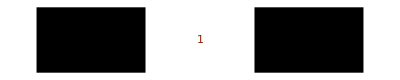

```mathematica
spec3=Sort[g2];
rect3=rect[#,0.2]&/@spec3;
st3=qToText[spec3,#,3,0]&/@G3;
show3={rect3,{comp,st3}};
Graphics[show3]
```

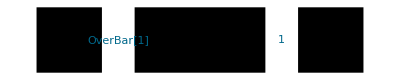

```mathematica
spec4=Sort[Last[rec[{g0,g1,g2},ts,tw]]];
rect4=rect[#,0.2]&/@spec4;
st4=qToText[spec4,#,4,0]&/@G4;
show4={rect4,{BostonBlue,st4}};
Graphics[show4]
```

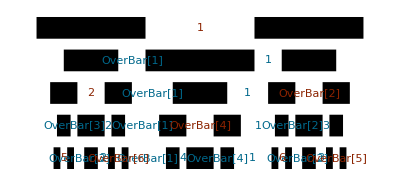

```mathematica
st=Directive[FontSize->11,FontFamily->"CMU Serif"];
δ=0.3;
Graphics[{show3,Translate[show4,{0,-δ}],Table[Translate[printGaps[i],{0,- δ i}],{i,2,4}]}]
```

```mathematica
Export[NotebookDirectory[]<>"gap_labels.pdf",%]
```

/home/nicolas/git/talks/ICQ13 September 2016/talk/img/gap_labels.pdf

```mathematica
printMainGaps[n_]:=Block[{spec,rects,i=n-2,stablegaps,transientgaps,txtstable,txttr,lbl0},
(* compute the spectrum *)
spec=Nest[rec[#,ts,tw]&,{g0,g1,g2},n]//Last;
spec=Sort[spec];
rects=rect[#,0.2]&/@spec;
(* compute the gap labels *)
transientgaps=Nest[recurtr,{G3tr,G4tr,G5tr},i]//Last;

(* print the two largest gaps *)
txtstable=qToText[spec,#,i+5,0]&/@{{1,-1},{0,1}};
(* select the label of the E=0 gap *)
lbl0=transientgaps[[Floor[(Length[transientgaps]+1)/2]]];
(* print the E=0 gap *)
txttr=qToText[spec,#,i+5,0]&/@{lbl0};
If[Mod[n,3]==0,
{rects,{BostonBlue,txtstable},{comp,txttr}},
{rects,{BostonBlue,txtstable}}]
]
```

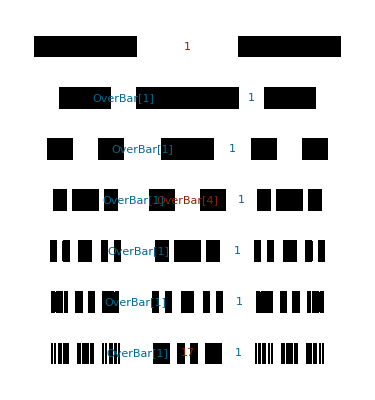

```mathematica
st=Directive[FontSize->9,FontFamily->"CMU Serif"];
δ=0.5;
Graphics[{show3,Translate[show4,{0,-δ}],Table[Translate[printMainGaps[i],{0,- δ i}],{i,2,6}]}]
```

```mathematica
Export[NotebookDirectory[]<>"main_gap_labels.pdf",%]
```

/home/nicolas/git/talks/ICQ13 September 2016/talk/img/main_gap_labels.pdf